```mathematica
λ=10;
q=(2Pi)/λ;
β=1;
```

```mathematica
μ[x_,u_,δ_]:=u+δ Sin[q x]; (* chemical potential μ as function of position x' (denoted simply x), equilibrium u, and perturbation δ *)
m[μ_]:=(Subscript[m, 0] Subscript[v, F]^2)/(β Subscript[v, F]^2 h^2(2Pi))(Log[1+E^(β μ)]+Log[1+E^(-β μ)]); (* total carrier density n_+ (named m) as function of chemical potential μ *)
n[μ_]:=1/(β^2 Subscript[v, F]^2 h^2(2Pi))(PolyLog[2,-E^(-β μ)]-PolyLog[2,-E^(β μ)]); (* carrier density difference n_- (named n) as function of chemical potential μ *)
```

```mathematica
(* Integral Calculations for Current Functions *)
A[u_,δ_]:=((β Subscript[v, F]^2 h^2(2Pi))/(Subscript[m, 0] Subscript[v, F]^2))(1/λ)NIntegrate[1/(Log[1+E^(β μ[t,u,δ])]+Log[1+E^(-β μ[t,u,δ])]),{t,0,λ}]; (* λ-average of 1/n_+ at equilibrium u and perturbation δ *)
B[u_,δ_]:=(1/(β Subscript[m, 0] Subscript[v, F]^2))(1/λ)NIntegrate[(PolyLog[2,-E^(-β μ[t,u,δ])]-PolyLog[2,-E^(β μ[t,u,δ])])/(Log[1+E^(β μ[t,u,δ])]+Log[1+E^(-β μ[t,u,δ])]),{t,0,λ}]; (* λ-average of n_-/n_+ at equilibrium u and perturbation δ *)


Subscript[I, X][x_,u_,δ_]:=e Subscript[v, s](n[μ[x,u,δ]]-B[u,δ]/A[u,δ]); (* current density j as function of position x, equilibrium u, and perturbation δ *)
Subscript[I, aec][u_,δ_]:=(e Subscript[v, s])(1/(β^2 Subscript[v, F]^2 h^2(2Pi)))(1/λ)NIntegrate[(PolyLog[2,-E^(-β μ[t,u,δ])]-PolyLog[2,-E^(β μ[t,u,δ])]),{t,0,λ}]-e Subscript[v, s] B[u,δ]/A[u,δ]; (* current λ-average J (DC current) as function of equilibrium u, and perturbation δ *)
Subscript[i, aec][u_,δ_]:=(β^2 h^2 Subscript[v, F]^2)/(e Subscript[v, s])J[u,δ]; (* DC current Subscript[J, aec] in graphable units *)
i[x_,u_,δ_]:=(β^2 h^2 Subscript[v, F]^2)/(e Subscript[v, s])j[x,u,δ];
```

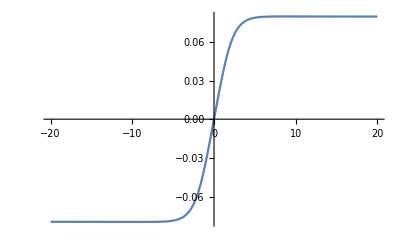

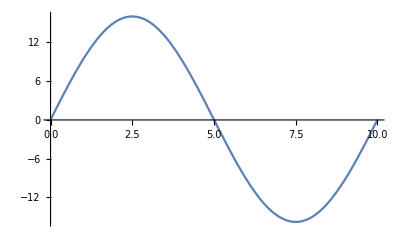

```mathematica
(* Acoustoelectric Current Plots *)
Plot[{Subscript[i, aec][u,1]},{u,-20,20},PlotLegends->"Expressions"]
Plot[i[x,100,1],{x,0,λ}]
```

```mathematica
(* Approximated Integral Calculations *)
l[x_,u_,δ_]:=e Subscript[v, s]((2β Log[2])/(β^2 Subscript[v, F]^2 h^2(2Pi))μ[x,u,δ]-((1/(β Subscript[m, 0] Subscript[v, F]^2))(1/λ)NIntegrate[((2β Log[2])μ[t,u,δ])/(2Log[2]+(β^2(μ[t,u,δ])^2)/4),{t,0,λ}])/(((β Subscript[v, F]^2 h^2(2Pi))/(Subscript[m, 0] Subscript[v, F]^2))(1/λ)NIntegrate[1/(2Log[2]+(β^2(μ[t,u,δ])^2)/4),{t,0,λ}])); (* approximated current density l *)
L[u_,δ_]:=(e Subscript[v, s])((2β Log[2])/(β^2 Subscript[v, F]^2 h^2(2Pi)))NIntegrate[(2β Log[2])μ[t,u,δ],{t,0,λ}]-e Subscript[v, s]((1/(β Subscript[m, 0] Subscript[v, F]^2))(1/λ)NIntegrate[((2β Log[2])μ[t,u,δ])/(2Log[2]+(β^2(μ[t,u,δ])^2)/4),{t,0,λ}])/(((β Subscript[v, F]^2 h^2(2Pi))/(Subscript[m, 0] Subscript[v, F]^2))(1/λ)NIntegrate[1/(2Log[2]+(β^2(μ[t,u,δ])^2)/4),{t,0,λ}]); (* λ-average of the approximate l *)
Subscript[L, aec][u_,δ_]:=(β^2 h^2 Subscript[v, F]^2)/(e Subscript[v, s])L[u,δ]; (* DC approximated current Subscript[L, aec] in graphable units *)
```

```mathematica
(* Series Approximations *)
?Series
Series[Log[1+E^(α μ)]+Log[1+E^(-α μ)],{μ,0,4}]
Series[PolyLog[2,-E^(-α μ)]-PolyLog[2,-E^(α μ)],{μ,0,4}]
```

2 Log[2]+(α^2 μ^2)/4-(α^4 μ^4)/96+O[μ]^5

2 α Log[2] μ+(α^3 μ^3)/12+O[μ]^5

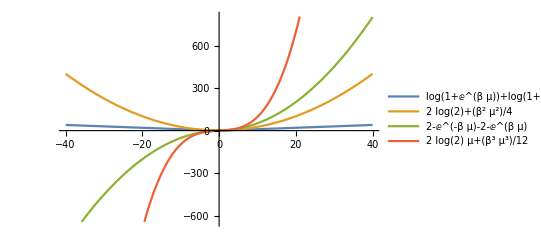

```mathematica
(* Series Approximation Plots *)
Plot[{(Log[1+E^(β μ)]+Log[1+E^(-β μ)]),2 Log[2]+(β^2 μ^2)/4,(PolyLog[2,-E^(-β μ)]-PolyLog[2,-E^(β μ)]),2 Log[2] μ+(β^3 μ^3)/12},{μ,-40,40},PlotLegends->"Expressions"]
```

```mathematica
j[u_,δ_,x_]:=(e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2)((PolyLog[2,-Exp[-β(u-δ Sin[q x])]]-PolyLog[2,-Exp[β(u-δ Sin[q x])]])-NIntegrate[(PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]])/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]/NIntegrate[1/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]); (* current solution as a function of u=Subscript[μ, 0], δ=δμ, x=x' *)
Subscript[j, aec][u_,δ_]:=(e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2)(1/λ NIntegrate[PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]],{t,0,λ}]-NIntegrate[(PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]])/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]/NIntegrate[1/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]); (* acoustoelectric current obtained by averaging j, function of u=Subscript[μ, 0], δ=δμ *)
```

```mathematica
Plot3D[((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 j[u,30,x],{x,0,λ},{u,-50,50},PlotLegends->"Expressions"]
```

-Graphics3D-

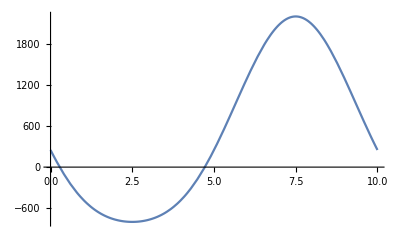

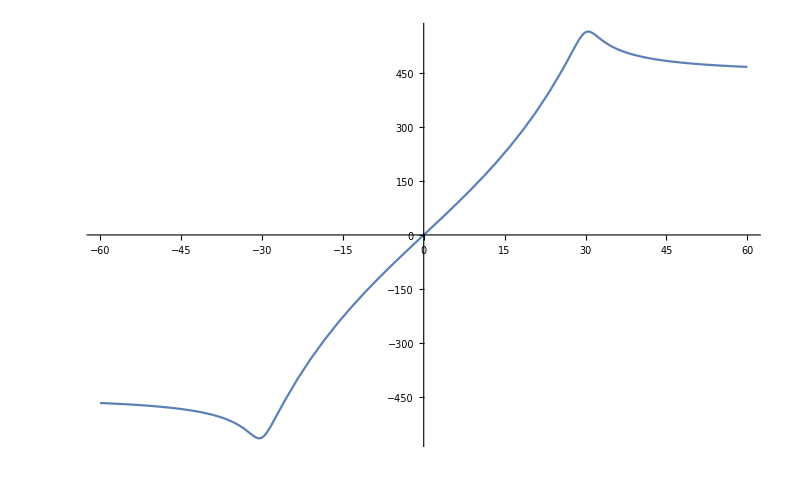

```mathematica
Plot[((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 j[50,30,x],{x,0,λ},PlotLegends->"Expressions"] (* plot of current j over a single wavelength for variable values of u=Subscript[μ, 0], δ=δμ *)
Plot[((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 Subscript[j, aec][u,30],{u,-60,60},PlotLegends->"Expressions"] (* plot of acoustoelectric current <j> over a range of equilibrium chemical potentials u=Subscript[μ, 0], for variable values of δ=δμ *)
```

```mathematica
a[u_,δ_]:=NIntegrate[(PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]])/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]/NIntegrate[1/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]; (* a[Subscript[μ, 0],δμ] = <n-/n+>/<1/n+> *)
b[u_,δ_]:=1/λ NIntegrate[PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]],{t,0,λ}]; (* b[Subscript[μ, 0],δμ] = <n- > *)
c[u_,δ_]:=1/λ NIntegrate[(PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]])/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]; (* c[Subscript[μ, 0],δμ] = <n-/n+> *)
d[u_,δ_]:=1/λ NIntegrate[1/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}] (* d[Subscript[μ, 0],δμ] = <1/n+> *)
```

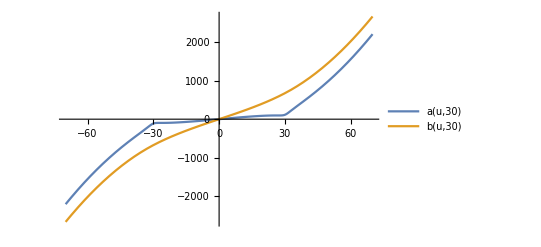

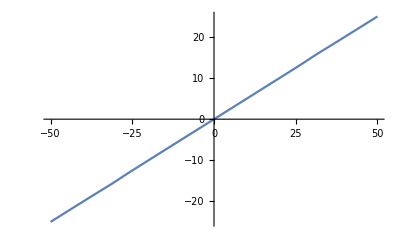

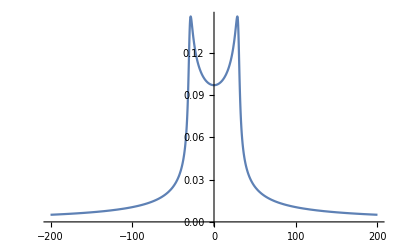

```mathematica
Plot[{a[u,30],b[u,30]},{u,-70,70},PlotLegends->"Expressions"]
(* Plot[{D[a[u,30],u],D[b[u,30],u]},{u,-50,50},PlotLegends->"Expressions"] *)
Plot[{c[u,30]},{u,-50,50},PlotLegends->"Expressions"]
Plot[{d[u,30]},{u,-200,200},PlotLegends->"Expressions"]
```